```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];SetOptions[$FrontEndSession,NotebookAutoSave->True];
NotebookSave[];
AppendTo[$Path,FileNameJoin[{$HomeDirectory,"Dropbox","EpidCRNmodels"}]];Needs["EpidCRN`"];
(*Latex dictionary*)
(*Human compartments*)Format[Nh,StandardForm]:=Subscript[N,h];
Format[Sh,StandardForm]:=Subscript[S,h];
Format[Id,StandardForm]:=Subscript[i,d];
Format[Iz,StandardForm]:=Subscript[i,z];
Format[Ic,StandardForm]:=Subscript[i,c];
Format[Rd,StandardForm]:=Subscript[R,d];
Format[Rz,StandardForm]:=Subscript[R,z];
Format[Jd,StandardForm]:=Subscript[J,d];
Format[Jz,StandardForm]:=Subscript[J,z];


(*Vector compartments*)
Format[Nv,StandardForm]:=Subscript[N,v];
Format[Sv,StandardForm]:=Subscript[S,v];
Format[Ivd,StandardForm]:=Subscript[i,vd];
Format[Ivz,StandardForm]:=Subscript[i,vz];
Format[Ivc,StandardForm]:=Subscript[i,vc];

(*PART 3:Subscript formatting for parameters*)

(*Death/birth rates*)
Format[mud,StandardForm]:=Subscript[μ,d];
Format[muz,StandardForm]:=Subscript[μ,z];
Format[muv,StandardForm]:=Subscript[μ,v];

(*Transmission rates*)
Format[behd,StandardForm]:=Subscript[β,hd];
Format[behz,StandardForm]:=Subscript[β,hz];
Format[bes,StandardForm]:=Subscript[β,s];
Format[bevd,StandardForm]:=Subscript[β,vd];
Format[bevz,StandardForm]:=Subscript[β,vz];

(*Recovery rates*)
Format[gad,StandardForm]:=Subscript[γ,d];
Format[gaz,StandardForm]:=Subscript[γ,z];
Format[gac,StandardForm]:=Subscript[γ,c];

(*Altered infectivity*)
Format[nud,StandardForm]:=Subscript[ν,d];
Format[nuz,StandardForm]:=Subscript[ν,z];

(*ADE parameters*)
Format[kd,StandardForm]:=Subscript[k,d];
Format[kz,StandardForm]:=Subscript[k,z];
Format[Id,StandardForm]:=Subscript[i,d];
Format[Iz,StandardForm]:=Subscript[i,z];
Format[Ic,StandardForm]:=Subscript[i,c];
Format[Idv,StandardForm]:=Subscript[i,dv];
Format[Izv,StandardForm]:=Subscript[i,zv];Format[Icv,StandardForm]:=Subscript[i,cv];
Format[Jd,StandardForm]:=Subscript[J,d];
Format[Jz,StandardForm]:=Subscript[J,z];
Format[Rd,StandardForm]:=Subscript[R,d];
Format[Rz,StandardForm]:=Subscript[R,z];
Format[Rc,StandardForm]:=Subscript[R,c];

(*Co-infection parameter*)
Format[rh,StandardForm]:=ρ;
Format[mu,StandardForm]:=μ;
Format[be,StandardForm]:=β;
Format[ga,StandardForm]:=γ;
Format[nu,StandardForm]:=ν;
(*Two-Strain Model with vaccination*)(*Species:Sh,Id,Iz,Ic,Rd,Rz,Jd,Jz,R (humans),Sv,Ivd,Ivz,Ivc (vectors)*)
RN={(*Human births and deaths*)0->"Sh","Sh"->0,"Id"->0,"Iz"->0,"Ic"->0,"Rd"->0,"Rz"->0,"Jd"->0,"Jz"->0,"Rc"->0,(*Vector births and deaths*)0->"Sv","Sv"->0,"Idv"->0,"Izv"->0,"Icv"->0,(*Susceptible human infections-dengue from vectors*)"Sh"+"Idv"->"Id"+"Idv","Sh"+"Icv"->"Id"+"Icv",(*Susceptible human infections-Zika from vectors*)"Sh"+"Izv"->"Iz"+"Izv","Sh"+"Icv"->"Iz"+"Icv",(*Susceptible human infections-Zika sexual transmission*)"Sh"+"Iz"->"Iz"+"Iz","Sh"+"Ic"->"Iz"+"Ic","Sh"+"Jz"->"Iz"+"Jz",(*Dengue-infected human coinfection with Zika*)"Id"+"Izv"->"Ic"+"Izv","Id"+"Icv"->"Ic"+"Icv","Id"+"Iz"->"Ic"+"Iz","Id"+"Ic"->2*"Ic","Id"+"Jz"->"Ic"+"Jz",(*Zika-infected human coinfection with dengue*)"Iz"+"Idv"->"Ic"+"Idv","Iz"+"Icv"->"Ic"+"Icv",(*Recoveries*)"Id"->"Rd","Iz"->"Rz","Ic"->"Jz","Ic"->"Jd","Jd"->"Rc","Jz"->"Rc",(*Dengue-recovered human infection with Zika*)"Rd"+"Izv"->"Jz"+"Izv","Rd"+"Icv"->"Jz"+"Icv","Rd"+"Iz"->"Jz"+"Iz","Rd"+"Ic"->"Jz"+"Ic","Rd"+"Jz"->2*"Jz",(*Zika-recovered human infection with dengue*)"Rz"+"Idv"->"Jd"+"Idv","Rz"+"Icv"->"Jd"+"Icv",(*Susceptible vector infections-dengue*)"Sv"+"Id"->"Idv"+"Id","Sv"+"Ic"->"Idv"+"Ic","Sv"+"Jd"->"Idv"+"Jd",(*Susceptible vector infections-Zika*)"Sv"+"Iz"->"Izv"+"Iz","Sv"+"Ic"->"Izv"+"Ic","Sv"+"Jz"->"Izv"+"Jz",(*Dengue-infected vector coinfection with Zika*)"Idv"+"Iz"->"Icv"+"Iz","Idv"+"Ic"->"Icv"+"Ic","Idv"+"Jz"->"Icv"+"Jz",(*Zika-infected vector coinfection with dengue*)"Izv"+"Id"->"Icv"+"Id","Izv"+"Ic"->"Icv"+"Ic","Izv"+"Jd"->"Icv"+"Jd"};

rts={(*1-10:Births and deaths of humans-NO denominators*)mu*Nh,(*0->Sh*)mu*Sh,(*Sh->0*)mu*Id,(*Id->0*)mu*Iz,(*Iz->0*)mu*Ic,(*Ic->0*)mu*Rd,(*Rd->0*)mu*Rz,(*Rz->0*)mu*Jd,(*Jd->0*)mu*Jz,(*Jz->0*)mu*Rc,(*Rc->0*)(*11-15:Births and deaths of vectors-NO denominators*)muv*Nv,(*0->Sv*)muv*Sv,(*Sv->0*)muv*Idv,(*Idv->0*)muv*Izv,(*Izv->0*)muv*Icv,(*Icv->0*)(*16-22:Sh infections-WITH/Nh*)behd*Sh*Idv/Nh,(*Sh+Idv->Id+Idv*)behd*nud*Sh*Icv/Nh,(*Sh+Icv->Id+Icv*)behz*Sh*Izv/Nh,(*Sh+Izv->Iz+Izv*)behz*nuz*Sh*Icv/Nh,(*Sh+Icv->Iz+Icv*)bes*Sh*Iz/Nh,(*Sh+Iz->Iz+Iz*)bes*Sh*Ic/Nh,(*Sh+Ic->Iz+Ic*)bes*kz*Sh*Jz/Nh,(*Sh+Jz->Iz+Jz*)(*23-29:Id and Iz coinfections-WITH/Nh*)rh*behz*Id*Izv/Nh,(*Id+Izv->Ic+Izv*)rh*behz*nuz*Id*Icv/Nh,(*Id+Icv->Ic+Icv*)rh*bes*Id*Iz/Nh,(*Id+Iz->Ic+Iz*)rh*bes*Id*Ic/Nh,(*Id+Ic->2*Ic*)rh*bes*kz*Id*Jz/Nh,(*Id+Jz->Ic+Jz*)rh*behd*Iz*Idv/Nh,(*Iz+Idv->Ic+Idv*)rh*behd*nud*Iz*Icv/Nh,(*Iz+Icv->Ic+Icv*)(*30-35:Recoveries-NO denominators*)gad*Id,(*Id->Rd*)gaz*Iz,(*Iz->Rz*)rh*gad*Ic,(*Ic->Jz*)rh*gaz*Ic,(*Ic->Jd*)gad*Jd,(*Jd->Rc*)gaz*Jz,(*Jz->Rc*)(*36-42:Rd and Rz infections-WITH/Nh*)behz*Rd*Izv/Nh,(*Rd+Izv->Jz+Izv*)behz*nuz*Rd*Icv/Nh,(*Rd+Icv->Jz+Icv*)bes*Rd*Iz/Nh,(*Rd+Iz->Jz+Iz*)bes*Rd*Ic/Nh,(*Rd+Ic->Jz+Ic*)bes*kz*Rd*Jz/Nh,(*Rd+Jz->2*Jz*)behd*Rz*Idv/Nh,(*Rz+Idv->Jd+Idv*)behd*nud*Rz*Icv/Nh,(*Rz+Icv->Jd+Icv*)(*43-48:Sv infections-WITH/Nh*)bevd*Sv*Id/Nh,(*Sv+Id->Idv+Id*)bevd*Sv*Ic/Nh,(*Sv+Ic->Idv+Ic*)bevd*kd*Sv*Jd/Nh,(*Sv+Jd->Idv+Jd*)bevz*Sv*Iz/Nh,(*Sv+Iz->Izv+Iz*)bevz*Sv*Ic/Nh,(*Sv+Ic->Izv+Ic*)bevz*kz*Sv*Jz/Nh,(*Sv+Jz->Izv+Jz*)(*49-54:Vector coinfections-WITH/Nh*)rh*bevz*Idv*Iz/Nh,(*Idv+Iz->Icv+Iz*)rh*bevz*Idv*Ic/Nh,(*Idv+Ic->Icv+Ic*)rh*bevz*kz*Idv*Jz/Nh,(*Idv+Jz->Icv+Jz*)rh*bevd*Izv*Id/Nh,(*Izv+Id->Icv+Id*)rh*bevd*Izv*Ic/Nh,(*Izv+Ic->Icv+Ic*)rh*bevd*kd*Izv*Jd/Nh      (*Izv+Jd->Icv+Jd*)};
Print[rts//Length," reactions and rates: ",Transpose[{RN,rts}]//MatrixForm]
{RHS, var, par, cp, mSi, Jx, Jy, E0, Kp, R0A, infV,ngm}=bdAn[RN,rts];
Print["E0 is",E0," mSi=",mSi," infV=",infV," the ",R0A//Length,"repr fns=",R0A]
```

54 reactions and rates: (0→Sh | μ N_h
Sh→0 | μ S_h
Id→0 | i_d μ
Iz→0 | i_z μ
Ic→0 | i_c μ
Rd→0 | μ R_d
Rz→0 | μ R_z
Jd→0 | J_d μ
Jz→0 | J_z μ
Rc→0 | μ R_c
0→Sv | μ_v N_v
Sv→0 | μ_v S_v
Idv→0 | i_dv μ_v
Izv→0 | i_zv μ_v
Icv→0 | i_cv μ_v
Idv+Sh→Id+Idv | (β_hd i_dv S_h)/N_h
Icv+Sh→Icv+Id | (β_hd i_cv ν_d S_h)/N_h
Izv+Sh→Iz+Izv | (β_hz i_zv S_h)/N_h
Icv+Sh→Icv+Iz | (β_hz i_cv ν_z S_h)/N_h
Iz+Sh→2 Iz | (β_s i_z S_h)/N_h
Ic+Sh→Ic+Iz | (β_s i_c S_h)/N_h
Jz+Sh→Iz+Jz | (β_s J_z k_z S_h)/N_h
Id+Izv→Ic+Izv | (β_hz i_d i_zv ρ)/N_h
Icv+Id→Ic+Icv | (β_hz i_cv i_d ν_z ρ)/N_h
Id+Iz→Ic+Iz | (β_s i_d i_z ρ)/N_h
Ic+Id→2 Ic | (β_s i_c i_d ρ)/N_h
Id+Jz→Ic+Jz | (β_s i_d J_z k_z ρ)/N_h
Idv+Iz→Ic+Idv | (β_hd i_dv i_z ρ)/N_h
Icv+Iz→Ic+Icv | (β_hd i_cv i_z ν_d ρ)/N_h
Id→Rd | γ_d i_d
Iz→Rz | γ_z i_z
Ic→Jz | γ_d i_c ρ
Ic→Jd | γ_z i_c ρ
Jd→Rc | γ_d J_d
Jz→Rc | γ_z J_z
Izv+Rd→Izv+Jz | (β_hz i_zv R_d)/N_h
Icv+Rd→Icv+Jz | (β_hz i_cv ν_z R_d)/N_h
Iz+Rd→Iz+Jz | (β_s i_z R_d)/N_h
Ic+Rd→Ic+Jz | (β_s i_c R_d)/N_h
Jz+Rd→2 Jz | (β_s J_z k_z R_d)/N_h
Idv+Rz→Idv+Jd | (β_hd i_dv R_z)/N_h
Icv+Rz→Icv+Jd | (β_hd i_cv ν_d R_z)/N_h
Id+Sv→Id+Idv | (β_vd i_d S_v)/N_h
Ic+Sv→Ic+Idv | (β_vd i_c S_v)/N_h
Jd+Sv→Idv+Jd | (β_vd J_d k_d S_v)/N_h
Iz+Sv→Iz+Izv | (β_vz i_z S_v)/N_h
Ic+Sv→Ic+Izv | (β_vz i_c S_v)/N_h
Jz+Sv→Izv+Jz | (β_vz J_z k_z S_v)/N_h
Idv+Iz→Icv+Iz | (β_vz i_dv i_z ρ)/N_h
Ic+Idv→Ic+Icv | (β_vz i_c i_dv ρ)/N_h
Idv+Jz→Icv+Jz | (β_vz i_dv J_z k_z ρ)/N_h
Id+Izv→Icv+Id | (β_vd i_d i_zv ρ)/N_h
Ic+Izv→Ic+Icv | (β_vd i_c i_zv ρ)/N_h
Izv+Jd→Icv+Jd | (β_vd i_zv J_d k_d ρ)/N_h)

mSi={{i_d,i_c,J_d,i_dv,i_cv},{i_z,i_c,J_z,i_zv,i_cv}}

E0 is{R_c→0,R_d→0,R_z→0,S_h→N_h,S_v→N_v,i_c→0,i_cv→0,i_d→0,i_dv→0,i_z→0,i_zv→0,J_d→0,J_z→0} infV={i_c,i_cv,i_d,i_dv,i_z,i_zv,J_d,J_z} the 2repr fns={(√β_hd √β_vd √(k_d R_z+S_h) √S_v)/(√(γ_d+μ) √μ_v N_h),(β_s γ_d k_z μ μ_v R_d+β_s k_z μ^2 μ_v R_d+β_s γ_d^2 k_z μ_v R_d ρ+β_s γ_d γ_z k_z μ_v R_d ρ+β_s γ_d k_z μ μ_v R_d ρ+β_s γ_z k_z μ μ_v R_d ρ+β_s γ_d μ μ_v S_h+β_s μ^2 μ_v S_h+β_s γ_d^2 μ_v ρ S_h+β_s γ_d γ_z μ_v ρ S_h+β_s γ_d μ μ_v ρ S_h+β_s γ_z μ μ_v ρ S_h+(γ_d+μ) √μ_v (μ+γ_d ρ+γ_z ρ) √(k_z R_d+S_h) √(β_s^2 k_z μ_v R_d+β_s^2 μ_v S_h+4 β_hz β_vz γ_z S_v+4 β_hz β_vz μ S_v))/(2 (γ_d+μ) (γ_z+μ) μ_v N_h (μ+γ_d ρ+γ_z ρ))}

```mathematica
R0A/.E0//Simplify
```

{(√β_hd √β_vd √N_v)/(√(γ_d+μ) √μ_v √N_h),(β_s+(√(β_s^2 μ_v N_h+4 β_hz β_vz (γ_z+μ) N_v))/(√μ_v √N_h))/(2 (γ_z+μ))}

```mathematica
per={1,2,3,4,7,5,6,8};Print["K=",K=Kp[[per,per]]//MatrixForm]
```

K=(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (β_hd ν_d S_h)/μ_v | 0 | (β_hd S_h)/μ_v | 0 | 0 | 0 | 0
(β_vd (γ_d+μ+γ_z k_d ρ) S_v)/((γ_d+μ) (μ+(γ_d+γ_z) ρ)) | 0 | (β_vd S_v)/(γ_d+μ) | 0 | (β_vd k_d S_v)/(γ_d+μ) | 0 | 0 | 0
0 | (β_hd ν_d R_z)/μ_v | 0 | (β_hd R_z)/μ_v | 0 | 0 | 0 | 0
(β_s (γ_z+μ+γ_d k_z ρ) S_h)/((γ_z+μ) (μ+(γ_d+γ_z) ρ)) | (β_hz ν_z S_h)/μ_v | 0 | 0 | 0 | (β_s S_h)/(γ_z+μ) | (β_hz S_h)/μ_v | (β_s k_z S_h)/(γ_z+μ)
(β_vz (γ_z+μ+γ_d k_z ρ) S_v)/((γ_z+μ) (μ+(γ_d+γ_z) ρ)) | 0 | 0 | 0 | 0 | (β_vz S_v)/(γ_z+μ) | 0 | (β_vz k_z S_v)/(γ_z+μ)
(β_s R_d (γ_z+μ+γ_d k_z ρ))/((γ_z+μ) (μ+(γ_d+γ_z) ρ)) | (β_hz ν_z R_d)/μ_v | 0 | 0 | 0 | (β_s R_d)/(γ_z+μ) | (β_hz R_d)/μ_v | (β_s k_z R_d)/(γ_z+μ))

```mathematica
R0A/.E0//Factor
```

{-(√β_hd √β_vd √N_h √N_v)/(√(γ_d+μ) √μ_v),(√β_hd √β_vd √N_h √N_v)/(√(γ_d+μ) √μ_v),(√N_h (β_s √μ_v √N_h-√(β_s^2 μ_v N_h+4 β_hz β_vz γ_z N_v+4 β_hz β_vz μ N_v)))/(2 (γ_z+μ) √μ_v),(√N_h (β_s √μ_v √N_h+√(β_s^2 μ_v N_h+4 β_hz β_vz γ_z N_v+4 β_hz β_vz μ N_v)))/(2 (γ_z+μ) √μ_v)}

```mathematica
{E1,E2,r12,r21,coP,fl}=invNr[E1t,E2t,R0A,E0,par,cp,2,4]
```

Error: in2 must be an integer between 1 and 2

Set::shape: Lists {E1,E2,R12,R21,coP,fl} and $Failed are not the same shape.

$Failed

```mathematica
(*eq=Thread[(RHS/.coP)==0];
so=Solve[eq,var]//FullSimplify;
Print[so//Length," sols at nr. col coP, one is positive",so//N]
p0val=par/.coP;
pos=fpHopf[RHS, var, par, p0val]*)
```

```mathematica
plotInd={1,2};
steTol=10^(-8);
staTol=10^(-10);
choTol=10^(-13);

(*Call scan using all the precomputed values from memory*)
Timing[{fPl,unC,res}=scan[RHS,var,par,coP,plotInd,mSi,Automatic,steTol,staTol,choTol,R01,R02,r12,r21];]

fPl
```

Auto-determined varInd: {1,3,6}

Susceptible: S

Strain 1 (first compartment): I1

Strain 2 (first compartment): Y2

Computing R01=1, R02=1 intersection point...

R01-R02 intersection at: β_1 = 1.98242, β_2 = 1.18939

Adjusted ranges: β_1 ∈ [0.001, 5.97818], β_2 ∈ [0.001, 3.02311]

Scanning 121 parameter combinations...

Checked 30 potential coexistence points

All Rij equations: {0.504434 β_1==1,0.840767 β_2==1,(0.0690938 (3.50924+10.3983 β_1) β_2)/β_1==1,-1/β_20.564822 β_1 (-0.634221+15.1758 β_2-2.75027 √(0.946947 (3.70527-3.11527 β_2) β_2+(-0.230603+5.84265 β_2)^2))==1}

DFE: 16 (13%)

E2: 40 (33%)

E1: 35 (29%)

EE-Stable: 30 (25%)

{0.78125,Null}

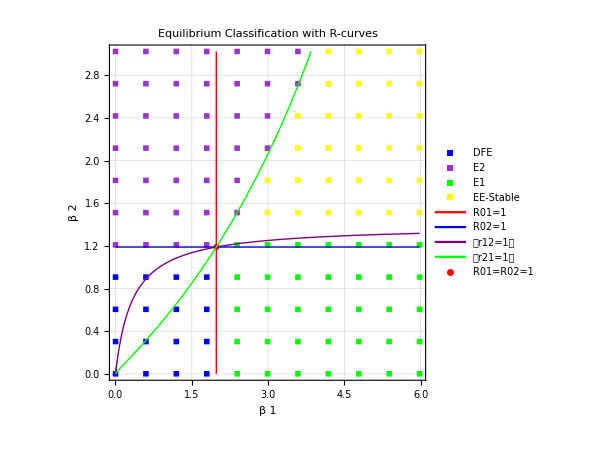

```mathematica
Export["BulhScan.pdf",fPl]
```

RahmanScan.pdf